## Mirror machine model with up-down asymmetry

```mathematica
Clear["Global`*"]
k = (2*π)/L;
AVertAsym[r_,θ_,z_]={0,(1/2.)*B0*r - ((B0*α)/k)*(Cos[k*z]*BesselI[1,k*r] +ϵ Sin[k*z/2]*BesselI[1,k*r/2]),0};
curlAVA[r_,θ_,z_]=Expand[Curl[AVertAsym[r,θ,z],{r,θ,z},"Cylindrical"]];
fieldVACyl[r_,θ_,z_]=Simplify[curlAVA[r,θ,z]//.{BesselI[1,2 π r/L]/r->( π /L)*(BesselI[0,2 π r/L]-BesselI[2,2 π r/L])}];
fieldVACyl[r_,θ_,z_] = fieldVACyl[r, θ, z]//.{BesselI[1,π r/L ]/r->(π /(2 L))*(BesselI[0,π r/L]-BesselI[2,π r/L])}//Simplify
fieldMagVACyl[r_,θ_,z_]=Sqrt[Dot[fieldVACyl[r,θ,z],fieldVACyl[r,θ,z]]]//.{BesselI[1,π r/L ]/r->(π /(2L))*(BesselI[0,π r/L]-BesselI[2,π r/L])}
bVACyl[r_,θ_,z_] =Simplify[fieldVACyl[r,θ,z]/fieldMagVACyl[r,θ,z]];
curlb[r_,θ_,z_] = Simplify[Curl[bVACyl[r,θ,z],{r,θ,z},"Cylindrical"]];
(*fieldVertAsymCar[x_,y_,z_]=fieldVertAsym[r,θ,z]//.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z}//Simplify*)
fieldVACar[x_,y_,z_] = {fieldVACyl[r,θ,z][[1]]*Cos[θ]-fieldVACyl[r,θ,z][[2]]*Sin[θ],
fieldVACyl[r,θ,z][[1]]*Sin[θ]+fieldVACyl[r,θ,z][[2]]*Cos[θ],
fieldVACyl[r,θ,z][[3]]}//.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z};
Sqrt[Dot[fieldVACar[x,y,z],fieldVACar[x,y,z]]];
fieldMagVACar[x_,y_,z_]=fieldMagVACyl[r,θ,z]//.{r-> Sqrt[x^2+y^2],θ->ArcTan[x,y],z-> z}
fieldMagVACar[x,y,L/2]
B0=1.0;α=0.5;L = π;ϵ=1.5;mutilde = 0.01;
```

{1/2 B0 α (ϵ BesselI[1,(π r)/L] Cos[(π z)/L]-2 BesselI[1,(2 π r)/L] Sin[(2 π z)/L]),0,-1. B0 (-1.+1. α BesselI[0,(2 π r)/L] Cos[(2 π z)/L]+0.5 α ϵ BesselI[0,(π r)/L] Sin[(π z)/L])}

√(1. B0^2 (-1.+1. α BesselI[0,(2 π r)/L] Cos[(2 π z)/L]+0.5 α ϵ BesselI[0,(π r)/L] Sin[(π z)/L])^2+1/4 B0^2 α^2 (ϵ BesselI[1,(π r)/L] Cos[(π z)/L]-2 BesselI[1,(2 π r)/L] Sin[(2 π z)/L])^2)

√(1. B0^2 (-1.+1. α BesselI[0,(2 π √(x^2+y^2))/L] Cos[(2 π z)/L]+0.5 α ϵ BesselI[0,(π √(x^2+y^2))/L] Sin[(π z)/L])^2+1/4 B0^2 α^2 (ϵ BesselI[1,(π √(x^2+y^2))/L] Cos[(π z)/L]-2 BesselI[1,(2 π √(x^2+y^2))/L] Sin[(2 π z)/L])^2)

1. √(B0^2 (-1.+0.5 α ϵ BesselI[0,(π √(x^2+y^2))/L]-1. α BesselI[0,(2 π √(x^2+y^2))/L])^2)

### Solving for the maxima and minimum in the field magnitude

```mathematica
saddleTop=FindMaximum[fieldMagVACyl[r,θ,z],{{r,0},{θ,0},{z,L/2.}}]
wellMid =FindMinimum[fieldMagVACyl[r,θ,z],{{r,0},{z,0.}}]
nullPt =FindMinimum[fieldMagVACyl[r,θ,z],{{r,1.},{z,0.}}]
saddleBot =FindMaximum[fieldMagVACyl[r,θ,z],{{r,0},{θ,0},{z,-L/2.}}]
h0=fieldMagVACyl[r,θ,z]/.saddleTop[[2]];
h1=fieldMagVACyl[r,θ,z]/.saddleBot[[2]];
(*Locating the points where |B| = 0*)
(*fieldZeroPt=FindRoot[fieldMagCylVA[r,0,0.1],{r,1.2}];
Print[fieldZeroPt,"; |B|=",fieldMagCylVA[r,0,0]/.fieldZeroPt ]*)
(*Locating the saddle points*)
(*fieldZeroPt=FindRoot[{D[fieldMagCylVA[r,0,z],r]==0,D[fieldMagCylVA[r,0,z],z]==0},{{r,-1.3},{z,0}}];
Print[fieldZeroPt,"; |B|=",fieldMagCylVA[r,0,0]/.fieldZeroPt ]*)
fieldMinPt = FindMinimum[fieldMagVACyl[r,θ,z],{{r,1.},{z,0.}},AccuracyGoal->10]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.125,{r→0.,θ→0.,z→1.5708}}

{0.464844,{r→0.,z→0.188616}}

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

{5.66275×10^-16,{r→0.884929,z→0.143259}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.875,{r→0.,θ→0.,z→-1.5708}}

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

{5.66275×10^-16,{r→0.884929,z→0.143259}}

### Plotting |B| contours, field lines, and |B| on the axis

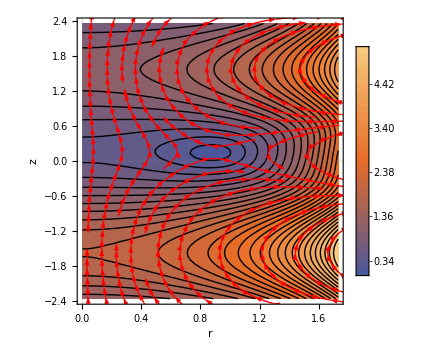

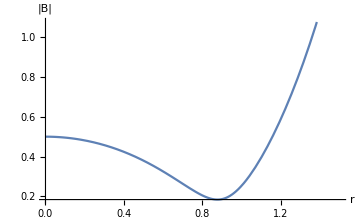
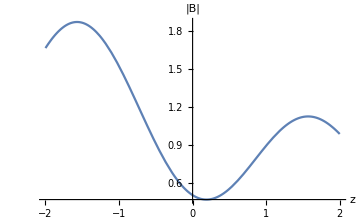

```mathematica
h0=fieldMagVACyl[r,θ,z]/.saddleTop[[2]];
h1=fieldMagVACyl[r,θ,z]/.saddleBot[[2]];
cplot2d =ContourPlot[fieldMagVACyl[r,0,z],{r,0,Sqrt[3]},{z,-1.5*(L/2),1.5*(L/2)},Contours->30,PlotPoints->10,MaxRecursion->2,PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->"Scientific",FrameLabel->{Style[r,20],Style[z,20]},ImageSize->Medium];
splot2d =StreamPlot[{fieldVACyl[r,0,z][[1]],fieldVACyl[r,0,z][[3]]},{r,0,2},{z,-2*(L/2),2*(L/2)},StreamColorFunction-> None,StreamStyle->Red,PlotLegends->Automatic,PlotTheme->"Scientific",FrameLabel->{Style[r,20],Style[z,20]},ImageSize->Medium];
Show[cplot2d,splot2d]
{Plot[fieldMagVACyl[r,0,0],{r,0,1.5},AxesLabel->{r,"|B|"},ImageSize->Medium],Plot[fieldMagVACyl[0,0,z],{z,-2,2},AxesLabel->{z,"|B|"},ImageSize->Medium]}
```

```mathematica
(*Energy[r,θ,z,vpar]=0.5*vpar^2+fieldMagVACyl[r,θ,z]
ContourPlot3D[Energy[r,0,z,vpar],{r,0,2.},{z,-1.5*(L/2),1.5*(L/2)},{vpar,-1,1},Contours->2,PlotPoints->10,MaxRecursion->2,ContourStyle->{Opacity[0.8]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[r,25],Style[z,25],Style[vpar,25]},AxesStyle->Directive[Gray,FontSize->15],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->300]*)
```

```mathematica
(*Export["~/Documents/magnetic-mirror/modB-axisym-z0asym.png",cplot2d,"PNG"]*)
cplot3d=ContourPlot3D[fieldMagVACyl[r,θ,z]+10.^-20,{r,0,2.},{θ,-2.*π,2.*π},{z,-1.5*(L/2),1.5*(L/2)},Contours->{h0+0.1*(h1-h0)},PlotPoints->10,MaxRecursion->2,ContourStyle->{Opacity[0.8]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[r,25],Style[θ,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->300]
```

-Graphics3D-

```mathematica
cplot3dCar=ContourPlot3D[fieldMagVACar[x,y,z],{x,-1.5,1.5},{y,-1.5,1.5},{z,-1,1.5*(π/k)},Contours->{h0+0.01},PlotPoints->10,MaxRecursion->2,ContourStyle->{Opacity[0.7]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->300]
```

-Graphics3D-

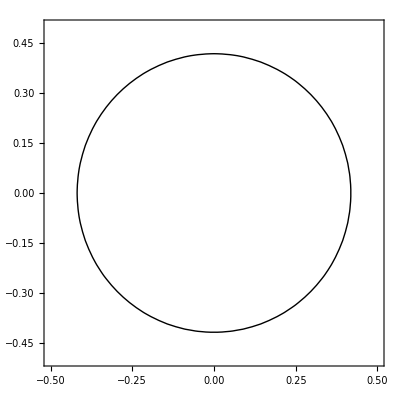

```mathematica
ContourPlot[fieldMagVACar[x,y,L/2],{x,-0.5,0.5},{y,-0.5,0.5},Contours->{h0+0.1*(h1-h0),h0+0.99*(h1-h0)},ContourShading->None]
```

### Hyperbolic periodic orbit and it’s manifolds of the first-order GCM

#### First order guiding center motion

```mathematica
modBCar[x_,y_,z_] = fieldMagVACar[x,y,z];
bVACar[x_,y_,z_] =Simplify[fieldVACar[x,y,z]/modBCar[x,y,z]];
gradModBCar[x_,y_,z_]= Simplify[Grad[modBCar[x,y,z],{x,y,z}]];
bCrossGradModB[x_,y_,z_] = Simplify[Cross[bVACar[x,y,z],gradModBCar[x,y,z]]];
curlbCar[x_,y_,z_] = Simplify[Curl[bVACar[x,y,z],{x,y,z}]];
tildeB[x_,y_,z_,vpar_]=fieldVACar[x,y,z] +Sqrt[mutilde]*vpar*curlbCar[x,y,z];
tildeBpar[x_,y_,z_,vpar_] = Dot[tildeB[x,y,z,vpar], bVACar[x,y,z]];
Eqn1=x'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[1]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn2=y'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[2]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn3=z'[t]==(vpar[t]*tildeB[x[t],y[t],z[t],vpar[t]][[3]] + Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
Eqn4=vpar'[t]==-(Dot[tildeB[x[t],y[t],z[t],vpar[t]],gradModBCar[x[t],y[t],z[t]]])/tildeBpar[x[t],y[t],z[t],vpar[t]];
eqpt=FindRoot[{Eqn1,Eqn2,Eqn3,Eqn4}/.{x'[t]->0,y'[t]->0,z'[t]->0,vpar'[t]->0},{{x[t],10.^-12},{y[t],10.^-12},{z[t],1.2},{vpar[t],0}}]
jacobianEOM=D[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
Chop[MatrixForm[jacobianEOM/.eqpt]]
{vals,vecs}=Eigensystem[N[Chop[jacobianEOM/.eqpt]]]
Det[N[Chop[jacobianEOM/.eqpt]]]
energyTopSaddle=fieldMagVACar[x[t],y[t],z[t]]/.eqpt[[1;;3]]
```

{x[t]→7.52316×10^-37,y[t]→7.52316×10^-37,z[t]→1.5708,vpar[t]→0.}

(0 | -0.0722222 | 0 | 0
0.0722222 | 0 | 0 | 0
0 | 0 | 0 | 1.
0 | 0 | 1.625 | 0)

{{-1.27475,1.27475,0.+0.0722222 ⅈ,0.-0.0722222 ⅈ},{{0.+0. ⅈ,0.+0. ⅈ,-0.617213+0. ⅈ,0.786796+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.617213+0. ⅈ,0.786796+0. ⅈ},{0.-0.707107 ⅈ,-0.707107+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0.707107 ⅈ,-0.707107+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}}}

-0.00847608

1.125

```mathematica
targetEnergy = energyTopSaddle+0.001
(*targetEnergy = h0+0.1*(h1-h0);*)
cplot3dCar=ContourPlot3D[fieldMagVACar[x,y,z],{x,-2.,2.},{y,-2.,2.},{z,-(π/k),(π/k)},Contours->{targetEnergy},PlotPoints->10,MaxRecursion->2,ContourStyle->{Opacity[0.8]},PlotLegends->Automatic,Mesh-> 5,MeshStyle->Gray,PlotTheme->{"Scientific"},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},ImageSize->300]
```

1.126

-Graphics3D-

#### Equations of motion for the PO on \Sigma^-

{0.,0.049596,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 86.7932 and t = 87.2119.

86.9498

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t],vpar[t]→InterpolatingFunction[…][t]}

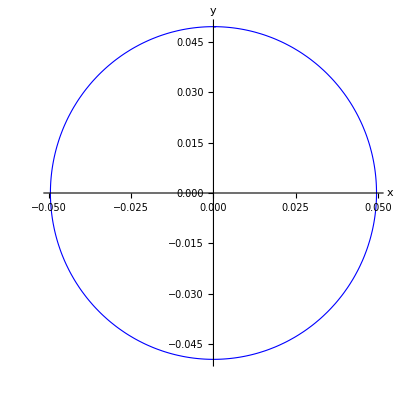

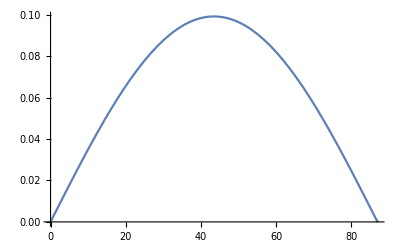

-Graphics3D-

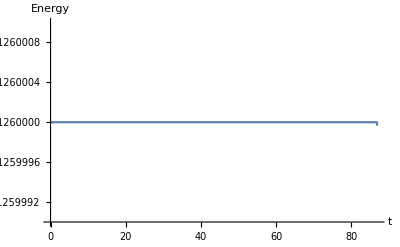

```mathematica
Clear[po,tEvent]
h0=fieldMagVACyl[r,θ,z]/.saddleTop[[2]];
h1=fieldMagVACyl[r,θ,z]/.saddleBot[[2]];
(*DOPRIamat={
{1/5},
{3/40,9/40},
{44/45,-56/15,32/9},
{19372/6561,-25360/2187,64448/6561,-212/729},
{9017/3168,-355/33,46732/5247,49/176,-5103/18656},
{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84, 0};
DOPRIcvec = {1/5,3/10,4/5,8/9,1, 1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5, p_]:=
N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec}, p];*)
zGuess = L/2.;xGuess = 0.;
yGuess =FindRoot[targetEnergy-fieldMagVACar[xGuess,y,zGuess],{y,0.6},AccuracyGoal->20][[1]][[2]];
guessCoord={xGuess,yGuess,zGuess,0.}
(*guessCoord = {0,0,1,0} +10.^-6*Re[vecs[[3]]]*)
tFinal =1.75*(2.*π)/RealAbs[Im[vals[[3]]]];
Eqn1SigmaMinus=x'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/fieldMagVACar[x[t],y[t],z[t]];
Eqn2SigmaMinus=y'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/fieldMagVACar[x[t],y[t],z[t]];
Eqn3SigmaMinus=z'[t]==(Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/fieldMagVACar[x[t],y[t],z[t]];
Eqn4SigmaMinus=vpar'[t]==0;
(*Eqn1SigmaMinus=x'[t]==(vpar[t]*fieldVACar[x[t],y[t],z[t]][[1]]+ Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[1]])/fieldMagVACar[x[t],y[t],z[t]];
Eqn2SigmaMinus=y'[t]==(vpar[t]*fieldVACar[x[t],y[t],z[t]][[2]]+ Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[2]])/fieldMagVACar[x[t],y[t],z[t]];
Eqn3SigmaMinus=z'[t]==(vpar[t]*fieldVACar[x[t],y[t],z[t]][[3]]+ Sqrt[mutilde]*bCrossGradModB[x[t],y[t],z[t]][[3]])/fieldMagVACar[x[t],y[t],z[t]];
Eqn4SigmaMinus =vpar'[t]==-Dot[fieldVACar[x[t],y[t],z[t]],gradModBCar[x[t],y[t],z[t]]]/fieldMagVACar[x[t],y[t],z[t]];*)
(*po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==guessCoord[[1]],y[0]==guessCoord[[2]],z[0]==guessCoord[[3]],vpar[0]==guessCoord[[4]]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}]*)
po=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==guessCoord[[1]],y[0]==guessCoord[[2]],z[0]==guessCoord[[3]],vpar[0]==guessCoord[[4]],WhenEvent[x[t]==0 && y[t] > 0.0,{Print[t],tEvent=t,"StopIntegration"},"DetectionMethod"->"DerivativeSign","LocationMethod"->"Brent"]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},AccuracyGoal->18,PrecisionGoal->30,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},InterpolationOrder->All]
(*tEvent =tFinal;*)
poPlot3d=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.po],{t,0,tEvent},AxesLabel->{x,y,z},LabelStyle->{25,GrayLevel[0]},PlotStyle->Directive[Blue,Thickness[0.01]]];
poPlot2d=ParametricPlot[Evaluate[{x[t],y[t]}/.po],{t,0,tEvent},AxesLabel->{x,y},LabelStyle->{10,GrayLevel[0]},PlotStyle->Directive[Blue,Thickness[0.002]]]
Plot[Norm[{x[t],y[t],z[t],vpar[t]}-guessCoord]/.po,{t,0,tEvent}]
(*Show[cplot3d,poPlot3d,PlotRange->{{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8 fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-0.8 fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8 fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-1.5*(L/2),1.5*(L/2)}}]*)
Show[cplot3dCar,poPlot3d,PlotRange->{{-1,1},{-1,1},{-2.*(π/k),2.*(π/k)}}]
Plot[(0.5*vpar[t]^2+fieldMagVACar[x[t],y[t],z[t]])/.po,{t,0,tEvent-0.1},PlotRange->{{0,tEvent},{targetEnergy-10.^-6,targetEnergy+10.^-6}},AxesLabel->{t,"Energy"}]
```

### Check the orbit is hyperbolic PO

```mathematica
tFinal = tEvent;
jacobianEOM=D[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
(*jacobianEOM=D[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},{{x[t],y[t],z[t],vpar[t]}}];*)
phiDot=Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]==Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]];
stmvf=Join[{Eqn1SigmaMinus[[1]],Eqn2SigmaMinus[[1]],Eqn3SigmaMinus[[1]],Eqn4SigmaMinus[[1]]},Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]]==Join[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]]];
(*stmvf=Join[{Eqn1[[1]],Eqn2[[1]],Eqn3[[1]],Eqn4[[1]]},Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]]==Join[{Eqn1[[2]],Eqn2[[2]],Eqn3[[2]],Eqn4[[2]]},Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]]];*)
ics = Join[{x[0],y[0],z[0],vpar[0]},Flatten[Table[ϕ[i,j][0],{i,4},{j,4}]]]==Join[{xGuess,yGuess,zGuess,0.},Flatten[IdentityMatrix[4]]];
vars = Join[{x,y,z,vpar},Flatten[Table[ϕ[i,j],{i,4},{j,4}]]];
sol=First@NDSolve[{stmvf,ics},vars,{t,0,tFinal},AccuracyGoal->16,PrecisionGoal->16,Method->{"ExplicitRungeKutta","DifferenceOrder"->8},InterpolationOrder->All]
(*sol =NDSolve[{stmvf,ics},vars,{t,0,tFinal},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->False}]*)
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…],vpar→InterpolatingFunction[…],ϕ[1,1]→InterpolatingFunction[…],ϕ[1,2]→InterpolatingFunction[…],ϕ[1,3]→InterpolatingFunction[…],ϕ[1,4]→InterpolatingFunction[…],ϕ[2,1]→InterpolatingFunction[…],ϕ[2,2]→InterpolatingFunction[…],ϕ[2,3]→InterpolatingFunction[…],ϕ[2,4]→InterpolatingFunction[…],ϕ[3,1]→InterpolatingFunction[…],ϕ[3,2]→InterpolatingFunction[…],ϕ[3,3]→InterpolatingFunction[…],ϕ[3,4]→InterpolatingFunction[…],ϕ[4,1]→InterpolatingFunction[…],ϕ[4,2]→InterpolatingFunction[…],ϕ[4,3]→InterpolatingFunction[…],ϕ[4,4]→InterpolatingFunction[…]}

```mathematica
phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.sol/.{t->tFinal};
{vals,vecs}=Eigensystem[phiMat1]
Clear[Wc,Ws,Wu,Ec,Es,Eu];
(*Re[vecs[[1]]]
Abs[vals[[3]]]
Print["|Ec|: ",Abs[vals[[2]]]]
Print["Re(w_lambda): ",Re[vecs[[1]]]]
Print["|w_omega)|: ",Norm[vecs[[2]]]]*)
Ec=ConstantArray[0,2];
Wc=ConstantArray[0,{2,4}];
k = 1;
For[i=1,i<=4,i++,
If[Abs[Im[vals[[i]]]]>10.^-20,
Ec[[k]]=vals[[i]];Wc[[k]]=Re[vecs[[i]]];k+=1,
If[Abs[vals[[i]]]<1,Es=vals[[i]],Eu=vals[[i]]]];
If[Re[vals[[i]]]-1<10.^-20&&Abs[Im[vals[[i]]]]<10.^-20,Es=vals[[i]];Ws=vecs[[i]],
Eu=vals[[i+1]];Wu=vecs[[i+1]]]]
Print[Ec," ",Wc]
Print[Es," ",Ws]
Print[Eu," ",Wu]
Eu=vals[[2]];Wu=vecs[[2]];
Es = vals[[3]];Ws=vecs[[3]];
```

{{1.,1.,1.,1.},{{1.,-4.9956×10^-7,0.,0.},{-1.60433×10^-15,1.90035×10^-14,1.,0.},{0.,0.,0.,1.},{1.,4.9956×10^-7,0.,0.}}}

{0,0} {{0,0,0,0},{0,0,0,0}}

1. {1.,4.9956×10^-7,0.,0.}

1. {-1.60433×10^-15,1.90035×10^-14,1.,0.}

### Differential correction of the hyperbolic PO

```mathematica
(*zGuess = L/2.;xGuess = 0.;
yGuess =FindRoot[h0+0.1*(h1-h0)-fieldMagVACar[xGuess,y,zGuess],{y,0.6},AccuracyGoal->20][[1]][[2]];
vparGuess=0.;
(*tFinal = (2.*π)/RealAbs[Im[vals[[3]]]]*)
jacobianEOM=D[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},{{x[t],y[t],z[t],vpar[t]}}];
phiDot=Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]==Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]];
stmvf=Join[{Eqn1SigmaMinus[[1]],Eqn2SigmaMinus[[1]],Eqn3SigmaMinus[[1]],Eqn4SigmaMinus[[1]]},Flatten[Table[ϕ[i,j]'[t],{i,4},{j,4}]]]==Join[{Eqn1SigmaMinus[[2]],Eqn2SigmaMinus[[2]],Eqn3SigmaMinus[[2]],Eqn4SigmaMinus[[2]]},Flatten[jacobianEOM.Table[ϕ[i,j][t],{i,4},{j,4}]]];
tpGuess = (2.*π)/RealAbs[Im[vals[[3]]]];
tFinal =0.5tpGuess;
maxIter = 10;numIter=0;maxdydot=10.^-30;
vparDot1=1; (*this assumes the guess initial condition is within 1 unit of the correct initial condition*)
While[numIter<maxIter&& Abs[vparDot1]>maxdydot,
initCondGuess = {xGuess,yGuess,zGuess,vparGuess};
vfSol=First@NDSolve[{Eqn1SigmaMinus,Eqn2SigmaMinus,Eqn3SigmaMinus,Eqn4SigmaMinus,x[0]==initCondGuess[[1]],y[0]==initCondGuess[[2]],z[0]==initCondGuess[[3]],vpar[0]==initCondGuess[[4]],WhenEvent[x[t]==0.,{"Stop Integration",tEvent=t}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinal},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
{x1,y1,z1,vpar1}={x[t],y[t],z[t],vpar[t]}/.vfSol/.t->tEvent;
Print[numIter,"   ",vparDot1,"   ",{xGuess,SetPrecision[yGuess,20],zGuess,vparGuess}];
ics = Join[{x[0],y[0],z[0],vpar[0]},Flatten[Table[ϕ[i,j][0],{i,4},{j,4}]]]==Join[{xGuess,yGuess,zGuess,0.},Flatten[IdentityMatrix[4]]];
vars = Join[{x,y,z,vpar},Flatten[Table[ϕ[i,j],{i,4},{j,4}]]];
stmvfSol=First@NDSolve[{stmvf,ics},vars,{t,0,tEvent},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];
phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->tEvent};
xDot1=Eqn1SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
yDot1=Eqn2SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
zDot1=Eqn3SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
vparDot1=Eqn4SigmaMinus[[2]]/.{x[t]->x1,y[t]->y1,z[t]->z1,vpar[t]->vpar1};
(*yGuessCorr =yDot1/(phiMat1[[4]][[2]]-phiMat1[[3]][[2]]*(zDot1/vparDot1));*)
yGuessCorr=((vpar1-0.)/(1.-phiMat1[[2]][[2]]))*(yDot1/vparDot1);
(*yGuessCorr =(x1-xDot1*(vpar1/vparDot1))/phiMat1[[1]][[2]];*)
Print[yGuessCorr];
yGuess = yGuess-yGuessCorr;
numIter++]*)
```

```mathematica
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.sol/.{t->tFinal};
{vals,vecs}=Eigensystem[phiMat1]
Re[vecs[[1]]]
Print["|Ec|: ",Abs[vals[[2]]]]
Print["Re(w_lambda): ",Re[vecs[[1]]]]
Print["|w_omega)|: ",Norm[vecs[[2]]]]*)
```

### Globalising the backward contracting (unstable) manifold

```mathematica
tpGuess = tEvent;
numTrajMani = 50;
idxTrajMani=1;
ti=0;deltati =tpGuess/numTrajMani;
uManiInitCond=ConstantArray[0,{numTrajMani,4}];
dir = -1;(*+1: directed towards positive z*)
del=10.^-12;
While[idxTrajMani<=numTrajMani && ti<tpGuess,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti};*)uManiInitCond[[idxTrajMani]]={x[t],y[t],z[t],vpar[t]}+dir*del*Re[Wu]/.po/.{t->ti};idxTrajMani++;ti=ti+deltati;]
(*Print[uManiInitCond//MatrixForm];*)
tFinalMani = 10*tpGuess;
ti=0;
uManiPlot3d=CreateDataStructure["DynamicArray"];
uManiIntersectParVel0 = ConstantArray[0,{idxTrajMani-1,4}];
For[idx=1,idx<idxTrajMani,idx++,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti+deltati};*)
Print[idx,": ",uManiInitCond[[idx]]];
uManiTraj=(*First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==uManiInitCond[[idx]][[1]],y[0]==uManiInitCond[[idx]][[2]],z[0]==uManiInitCond[[idx]][[3]],vpar[0]==uManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,uManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinalMani},MaxStepSize->0.001,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];*)
First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==uManiInitCond[[idx]][[1]],y[0]==uManiInitCond[[idx]][[2]],z[0]==uManiInitCond[[idx]][[3]],vpar[0]==uManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,uManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,tFinalMani},AccuracyGoal->16,Method->{"ExplicitRungeKutta","DifferenceOrder"->8,"StiffnessTest"->False},InterpolationOrder->All];
uManiPlot3d["Append",ParametricPlot3D[{x[t],y[t],z[t]}/.uManiTraj,{t,0,time2vparzero},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Magenta,Thickness[0.002]]]]
]
uManiIntersectParVel0 = Append[uManiIntersectParVel0,uManiIntersectParVel0[[1]]];
```

1: {1.69407×10^-21,0.049596,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 23.8065 and t = 24.09.

23.8679

2: {-0.00621603,0.0492049,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 23.7363 and t = 23.9739.

23.8679

3: {-0.012334,0.0480379,1.5708,0.}

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 23.6763 and t = 23.8908.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

23.8679

4: {-0.0182575,0.0461132,1.5708,0.}

23.8679

5: {-0.0238931,0.0434613,1.5708,0.}

23.8679

6: {-0.0291518,0.040124,1.5708,0.}

23.8679

7: {-0.0339508,0.0361539,1.5708,0.}

23.8679

8: {-0.0382144,0.0316137,1.5708,0.}

23.8679

9: {-0.0418753,0.0265749,1.5708,0.}

23.8679

10: {-0.0448758,0.021117,1.5708,0.}

23.8679

11: {-0.0471686,0.015326,1.5708,0.}

23.8679

12: {-0.0487175,0.00929336,1.5708,0.}

23.8679

13: {-0.0494981,0.00311416,1.5708,0.}

23.8679

14: {-0.0494981,-0.00311416,1.5708,0.}

23.8679

15: {-0.0487175,-0.00929336,1.5708,0.}

23.8679

16: {-0.0471686,-0.015326,1.5708,0.}

23.8679

17: {-0.0448758,-0.021117,1.5708,0.}

23.8679

18: {-0.0418753,-0.0265749,1.5708,0.}

23.8679

19: {-0.0382144,-0.0316137,1.5708,0.}

23.8679

20: {-0.0339508,-0.0361539,1.5708,0.}

23.8679

21: {-0.0291518,-0.040124,1.5708,0.}

23.8679

22: {-0.0238931,-0.0434613,1.5708,0.}

23.8679

23: {-0.0182575,-0.0461132,1.5708,0.}

23.8679

24: {-0.012334,-0.0480379,1.5708,0.}

23.8679

25: {-0.00621603,-0.0492049,1.5708,0.}

23.8679

26: {5.92245×10^-17,-0.049596,1.5708,0.}

23.8679

27: {0.00621603,-0.0492049,1.5708,0.}

23.8679

28: {0.012334,-0.0480379,1.5708,0.}

23.8679

29: {0.0182575,-0.0461132,1.5708,0.}

23.8679

30: {0.0238931,-0.0434613,1.5708,0.}

23.8679

31: {0.0291518,-0.040124,1.5708,0.}

23.8679

32: {0.0339508,-0.0361539,1.5708,0.}

23.8679

33: {0.0382144,-0.0316137,1.5708,0.}

23.8679

34: {0.0418753,-0.0265749,1.5708,0.}

23.8679

35: {0.0448758,-0.021117,1.5708,0.}

23.8679

36: {0.0471686,-0.015326,1.5708,0.}

23.8679

37: {0.0487175,-0.00929336,1.5708,0.}

23.8679

38: {0.0494981,-0.00311416,1.5708,0.}

23.8679

39: {0.0494981,0.00311416,1.5708,0.}

23.8679

40: {0.0487175,0.00929336,1.5708,0.}

23.8679

41: {0.0471686,0.015326,1.5708,0.}

23.8679

42: {0.0448758,0.021117,1.5708,0.}

23.8679

43: {0.0418753,0.0265749,1.5708,0.}

23.8679

44: {0.0382144,0.0316137,1.5708,0.}

23.8679

45: {0.0339508,0.0361539,1.5708,0.}

23.8679

46: {0.0291518,0.040124,1.5708,0.}

23.8679

47: {0.0238931,0.0434613,1.5708,0.}

23.8679

48: {0.0182575,0.0461132,1.5708,0.}

23.8679

49: {0.012334,0.0480379,1.5708,0.}

23.8679

50: {0.00621603,0.0492049,1.5708,0.}

23.8679

```mathematica
Show[cplot3dCar,poPlot3d,ListPointPlot3D[uManiIntersectParVel0[[All,1;;3]]],Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],PlotRange->{{-0.2,0.2},{-0.2,0.2},{-1,1.75}},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],ImageSize->500]
```

-Graphics3D-

### Globalising the forward contracting (stable) manifold

```mathematica
idxTrajMani=1;
dir = 1; (* -1: directed towards positive z*)
del=10.^-12;
ti=0;deltati =tpGuess/numTrajMani;
sManiInitCond=ConstantArray[0,{numTrajMani,4}];
While[idxTrajMani<=numTrajMani && ti<tpGuess,
sManiInitCond[[idxTrajMani]]={x[t],y[t],z[t],vpar[t]}+dir*del*Re[Ws]/.po/.{t->ti};
idxTrajMani++;
ti=ti+deltati;]
(*Print[sManiInitCond];*)
tFinalMani = 10.*tpGuess;
ti=0;
sManiPlot3d=CreateDataStructure["DynamicArray"];
sManiIntersectParVel0 = ConstantArray[0,{idxTrajMani-1,4}];
For[idx=1,idx<idxTrajMani,idx++,
(*phiMat1=Table[ϕ[i,j][t],{i,4},{j,4}]/.stmvfSol/.{t->ti+deltati};*)
Print[idx,": ",sManiInitCond[[idx]]];
sManiTraj=(*First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==sManiInitCond[[idx]][[1]],y[0]==sManiInitCond[[idx]][[2]],z[0]==sManiInitCond[[idx]][[3]],vpar[0]==sManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,sManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,-tFinalMani,0},MaxStepSize->0.01,Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients, "StiffnessTest"->True}];*)
First@NDSolve[{Eqn1,Eqn2,Eqn3,Eqn4,x[0]==sManiInitCond[[idx]][[1]],y[0]==sManiInitCond[[idx]][[2]],z[0]==sManiInitCond[[idx]][[3]],vpar[0]==sManiInitCond[[idx]][[4]],WhenEvent[vpar[t]==0,{"StopIntegration",time2vparzero=t,sManiIntersectParVel0[[idx]]={x[t],y[t],z[t],vpar[t]},Print[t]}]},{x[t],y[t],z[t],vpar[t]},{t,0,-tFinalMani},AccuracyGoal->16,Method->{"ExplicitRungeKutta","DifferenceOrder"->8,"StiffnessTest"->False},InterpolationOrder->All];
sManiPlot3d["Append",ParametricPlot3D[{x[t],y[t],z[t]}/.sManiTraj,{t,time2vparzero,0},AxesLabel->{x,y,z},PlotRange->{{-1,1},{-1,1},{-1,1}},LabelStyle->{20,GrayLevel[0]},PlotStyle->Directive[Green,Thickness[0.002]]]]
]
sManiIntersectParVel0=Append[sManiIntersectParVel0,sManiIntersectParVel0[[1]]];
```

1: {1.69407×10^-21,0.049596,1.5708,1.×10^-12}

-24.0588

2: {-0.00621603,0.0492049,1.5708,1.×10^-12}

-24.0587

3: {-0.012334,0.0480379,1.5708,1.×10^-12}

-24.0587

4: {-0.0182575,0.0461132,1.5708,1.×10^-12}

-24.0587

5: {-0.0238931,0.0434613,1.5708,1.×10^-12}

-24.0587

6: {-0.0291518,0.040124,1.5708,1.×10^-12}

-24.0587

7: {-0.0339508,0.0361539,1.5708,1.×10^-12}

-24.0587

8: {-0.0382144,0.0316137,1.5708,1.×10^-12}

-24.0587

9: {-0.0418753,0.0265749,1.5708,1.×10^-12}

-24.0587

10: {-0.0448758,0.021117,1.5708,1.×10^-12}

-24.0587

11: {-0.0471686,0.015326,1.5708,1.×10^-12}

-24.0587

12: {-0.0487175,0.00929336,1.5708,1.×10^-12}

-24.0587

13: {-0.0494981,0.00311416,1.5708,1.×10^-12}

-24.0587

14: {-0.0494981,-0.00311416,1.5708,1.×10^-12}

-24.0587

15: {-0.0487175,-0.00929336,1.5708,1.×10^-12}

-24.0587

16: {-0.0471686,-0.015326,1.5708,1.×10^-12}

-24.0587

17: {-0.0448758,-0.021117,1.5708,1.×10^-12}

-24.0587

18: {-0.0418753,-0.0265749,1.5708,1.×10^-12}

-24.0587

19: {-0.0382144,-0.0316137,1.5708,1.×10^-12}

-24.0587

20: {-0.0339508,-0.0361539,1.5708,1.×10^-12}

-24.0587

21: {-0.0291518,-0.040124,1.5708,1.×10^-12}

-24.0587

22: {-0.0238931,-0.0434613,1.5708,1.×10^-12}

-24.0587

23: {-0.0182575,-0.0461132,1.5708,1.×10^-12}

-24.0587

24: {-0.012334,-0.0480379,1.5708,1.×10^-12}

-24.0587

25: {-0.00621603,-0.0492049,1.5708,1.×10^-12}

-24.0587

26: {5.92245×10^-17,-0.049596,1.5708,1.×10^-12}

-24.0588

27: {0.00621603,-0.0492049,1.5708,1.×10^-12}

-24.0587

28: {0.012334,-0.0480379,1.5708,1.×10^-12}

-24.0587

29: {0.0182575,-0.0461132,1.5708,1.×10^-12}

-24.0587

30: {0.0238931,-0.0434613,1.5708,1.×10^-12}

-24.0587

31: {0.0291518,-0.040124,1.5708,1.×10^-12}

-24.0587

32: {0.0339508,-0.0361539,1.5708,1.×10^-12}

-24.0587

33: {0.0382144,-0.0316137,1.5708,1.×10^-12}

-24.0587

34: {0.0418753,-0.0265749,1.5708,1.×10^-12}

-24.0587

35: {0.0448758,-0.021117,1.5708,1.×10^-12}

-24.0587

36: {0.0471686,-0.015326,1.5708,1.×10^-12}

-24.0587

37: {0.0487175,-0.00929336,1.5708,1.×10^-12}

-24.0587

38: {0.0494981,-0.00311416,1.5708,1.×10^-12}

-24.0587

39: {0.0494981,0.00311416,1.5708,1.×10^-12}

-24.0587

40: {0.0487175,0.00929336,1.5708,1.×10^-12}

-24.0587

41: {0.0471686,0.015326,1.5708,1.×10^-12}

-24.0587

42: {0.0448758,0.021117,1.5708,1.×10^-12}

-24.0587

43: {0.0418753,0.0265749,1.5708,1.×10^-12}

-24.0587

44: {0.0382144,0.0316137,1.5708,1.×10^-12}

-24.0587

45: {0.0339508,0.0361539,1.5708,1.×10^-12}

-24.0587

46: {0.0291518,0.040124,1.5708,1.×10^-12}

-24.0587

47: {0.0238931,0.0434613,1.5708,1.×10^-12}

-24.0587

48: {0.0182575,0.0461132,1.5708,1.×10^-12}

-24.0587

49: {0.012334,0.0480379,1.5708,1.×10^-12}

-24.0587

50: {0.00621603,0.0492049,1.5708,1.×10^-12}

-24.0587

```mathematica
(*Show[cplot3d,poPlot3d,ListPointPlot3D[sManiIntersectParVel0[[All,1;;3]],PlotStyle->Green],ListPointPlot3D[uManiIntersectParVel0[[All,1;;3]],PlotStyle->Magenta],Table[sManiPlot3d["Part",idx],{idx,1,numTrajMani}],Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],PlotRange->{{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2],0.8*fieldMinPt[[2]][[All,2]][[1]]/Sqrt[2]},{-1.,1.}},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],ImageSize->500]*)
Show[cplot3dCar,poPlot3d,ListPointPlot3D[sManiIntersectParVel0[[All,1;;3]],PlotStyle->Green],ListPointPlot3D[uManiIntersectParVel0[[All,1;;3]],PlotStyle->Magenta],Table[uManiPlot3d["Part",idx],{idx,1,numTrajMani}],Table[sManiPlot3d["Part",idx],{idx,1,numTrajMani}],PlotRange->{{Min[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]-0.05,Max[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]+0.05},{Min[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]-0.05,Max[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]+0.05},{-1,2.0}},AxesLabel->{Style[x,25],Style[y,25],Style[z,25]},AxesStyle->Directive[Gray,FontSize->15],AspectRatio->2,ImageSize->500]
```

-Graphics3D-

-Graphics3D-

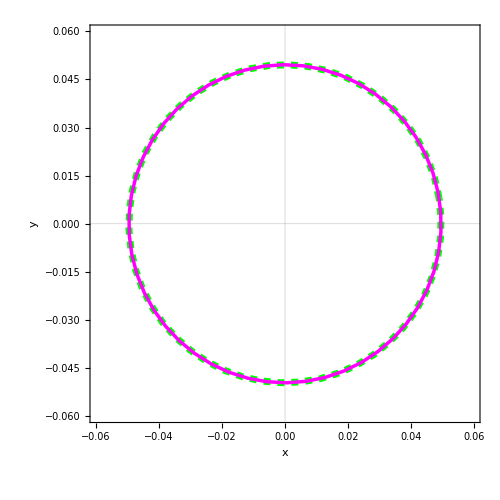

```mathematica
offset = 0.01;
Show[cplot3dCar,ListLinePlot3D[sManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Green,Dashed,Thickness[0.02]]],ListLinePlot3D[uManiIntersectParVel0[[All,1;;3]],PlotStyle->Directive[Magenta,Thickness[0.01]]],PlotRange->{{Min[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]-offset,Max[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]+offset},{Min[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]-offset,Max[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]+offset},{-0.70,-0.65}},AxesLabel->{Style[x,35],Style[y,35],Style[z,35]},AxesStyle->Directive[Gray,FontSize->18],ImageSize->500]
Show[{ListLinePlot[sManiIntersectParVel0[[All,1;;2]],PlotStyle->Directive[Green,Dashed,Thickness[0.01]],PlotTheme->{"Scientific"}],ListLinePlot[uManiIntersectParVel0[[All,1;;2]],PlotStyle->Directive[Magenta,Thickness[0.005]],PlotTheme->{"Scientific"}]},PlotRange->{{Min[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]-offset,Max[{sManiIntersectParVel0[[All,1]],uManiIntersectParVel0[[All,1]]}]+offset},{Min[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]-offset,Max[{sManiIntersectParVel0[[All,2]],uManiIntersectParVel0[[All,2]]}]+offset}},FrameLabel->{Style[x,35],Style[y,35]},FrameStyle->Directive[Gray,FontSize->15],AspectRatio->Equal,ImageSize->500]
```